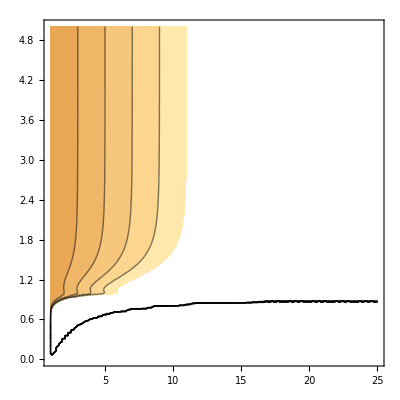

7936.

```mathematica
V[x_]:=(1/x)^12-2(1/x)^6;
Hc[n_, μ_] := (n-1) + V[1+(μ-1)n];
He[n_, μ_] := n V[μ];
ContourPlot[Hc[n, μ]-He[n, μ], {n, 1, 25}, {μ, 0, 5}, PlotRange->{-10, 10}]
He[2, 0.5]
```